```mathematica
SetDirectory[NotebookDirectory[]]
```

/Volumes/zitko-f1home/repos/tensor/test/susceptibility/tau-wr=0

```mathematica
<<sneg`;
```

sneg 1.252 Copyright (C) 2002-2019 Rok Zitko

a::shdw: Symbol a appears in multiple contexts {Sneg`,Global`}; definitions in context Sneg` may shadow or be shadowed by other definitions.

```mathematica
snegfermionoperators[c,d];
snegrealconstants[nu];
```

```mathematica
n=2;
ddd=2/n;
bz=qsbasisvc[{c[1],c[2],d[]}];
bz=Map[{#[[1]]+{n+1,0},#[[2]]}&,bz];
```

```mathematica
-1.+ddd/2
```

-0.5

```mathematica
ClearAll[ϵ];U=.;nu=.;t=.;V=.;
H=U/2 pow[number[d]-nu, 2]+U/2-U/2nu^2+Sum[ϵ[i] number[c[i]],{i,n}]+V Sum[nc[c[CR,i,UP],c[CR,i,DO],c[AN,j,DO],c[AN,j,UP]],{i,n},{j,n}]+t Sum[hop[c[i],d[]],{i,n}]//Expand
ϵ[1]=-1/2;
ϵ[2]=1/2;
U=10;
gamma=1;
V=Sqrt[2. gamma/Pi]
t=V/Sqrt[n]
α=1;
V=-α ddd;
H
mats=makematricesbzvc[H,bz]
```

U/2+t c_(1↓)^†·d_↓^+t c_(1⇑)^†·d_⇑^+t c_(2↓)^†·d_↓^+t c_(2⇑)^†·d_⇑^+t d_↓^†·c_(1↓)^+t d_↓^†·c_(2↓)^+1/2 U d_↓^†·d_↓^-nu U d_↓^†·d_↓^+t d_⇑^†·c_(1⇑)^+t d_⇑^†·c_(2⇑)^+1/2 U d_⇑^†·d_⇑^-nu U d_⇑^†·d_⇑^-V c_(1↓)^†·c_(1⇑)^†·c_(1↓)^·c_(1⇑)^-V c_(1↓)^†·c_(1⇑)^†·c_(2↓)^·c_(2⇑)^-V c_(2↓)^†·c_(2⇑)^†·c_(1↓)^·c_(1⇑)^-V c_(2↓)^†·c_(2⇑)^†·c_(2↓)^·c_(2⇑)^-U d_↓^†·d_⇑^†·d_↓^·d_⇑^+c_(1↓)^†·c_(1↓)^ ϵ[1]+c_(1⇑)^†·c_(1⇑)^ ϵ[1]+c_(2↓)^†·c_(2↓)^ ϵ[2]+c_(2⇑)^†·c_(2⇑)^ ϵ[2]

0.797885

0.56419

5-1/2 c_(1↓)^†·c_(1↓)^+0.56419 c_(1↓)^†·d_↓^-1/2 c_(1⇑)^†·c_(1⇑)^+0.56419 c_(1⇑)^†·d_⇑^+1/2 c_(2↓)^†·c_(2↓)^+0.56419 c_(2↓)^†·d_↓^+1/2 c_(2⇑)^†·c_(2⇑)^+0.56419 c_(2⇑)^†·d_⇑^+0.56419 d_↓^†·c_(1↓)^+0.56419 d_↓^†·c_(2↓)^+5 d_↓^†·d_↓^-10 nu d_↓^†·d_↓^+0.56419 d_⇑^†·c_(1⇑)^+0.56419 d_⇑^†·c_(2⇑)^+5 d_⇑^†·d_⇑^-10 nu d_⇑^†·d_⇑^+c_(1↓)^†·c_(1⇑)^†·c_(1↓)^·c_(1⇑)^+c_(1↓)^†·c_(1⇑)^†·c_(2↓)^·c_(2⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(1↓)^·c_(1⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(2↓)^·c_(2⇑)^-10 d_↓^†·d_⇑^†·d_↓^·d_⇑^

{{{0,0},{{5}}},{{1,1/2},{{10.-10 nu,0.56419,0.56419},{0.56419,5.5,0.},{0.56419,0.,4.5}}},{{2,0},{{25.-20 nu,0.797885,0.797885,0.,0.,0.},{0.797885,-10. (-1.05+nu),0.,0.797885,0.56419,0.},{0.797885,0.,-10. (-0.95+nu),0.,0.56419,0.797885},{0.,0.797885,0.,5.,0.,-1.},{0.,0.56419,0.56419,0.,5.,0.},{0.,0.,0.797885,-1.,0.,3.}}},{{2,1},{{10.5-10 nu,0.,-0.56419},{0.,9.5-10 nu,0.56419},{-0.56419,0.56419,5.}}},{{3,1/2},{{25.5-20 nu,0.,-0.56419,-0.398942,0.,-0.690988,0.,0.},{0.,24.5-20 nu,0.,-0.398942,-0.56419,0.690988,0.,0.},{-0.56419,0.,10.-10 nu,0.,-1.,0.,0.56419,0.},{-0.398942,-0.398942,0.,-10. (-1.+nu),0.,0.,-0.398942,-0.398942},{0.,-0.56419,-1.,0.,8.-10 nu,0.,0.,0.56419},{-0.690988,0.690988,0.,0.,0.,-10. (-1.+nu),0.690988,-0.690988},{0.,0.,0.56419,-0.398942,0.,0.690988,4.5,0.},{0.,0.,0.,-0.398942,0.56419,-0.690988,0.,3.5}}},{{3,3/2},{{-10 (-1+nu)}}},{{4,0},{{25.-20 nu,0.,-1.,0.797885,0.,0.},{0.,-20. (-1.25+nu),0.,-0.56419,-0.56419,0.},{-1.,0.,23.-20 nu,0.,0.797885,0.},{0.797885,-0.56419,0.,-10. (-0.95+nu),0.,0.797885},{0.,-0.56419,0.797885,0.,-10. (-0.85+nu),0.797885},{0.,0.,0.,0.797885,0.797885,3.}}},{{4,1},{{25.-20 nu,-0.56419,0.56419},{-0.56419,9.5-10 nu,0.},{0.56419,0.,8.5-10 nu}}},{{5,1/2},{{24.5-20 nu,0.,-0.56419},{0.,23.5-20 nu,-0.56419},{-0.56419,-0.56419,8.-10 nu}}},{{6,0},{{23-20 nu}}}}

```mathematica
matn=matrixrepresentationvc[number[d[]],bz[[5,2]]];
MatrixForm[matn]
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ClearAll[calc,calc0];
sub=5;
calc0[x_]:=calc0[x]=Module[{},
nu=x;
eps=U(1/2-x);
{qn,hh}=mats[[sub]];
bas=bz[[5,2]];
{val,vec}=Transpose@Sort@Transpose@Eigensystem[hh];
ω0j=val-First[val];
gij=vec.matn.ConjugateTranspose[vec];
χ=Sum[gij[[1,j]]^2(-1/(ω0j[[j]]-z)-1/(ω0j[[j]]+z)),{j,2,8}];
χ1=Sum[gij[[1,j]]^2(-1/(ω0j[[j]]-z)),{j,1,8}];
χ2=Sum[gij[[1,j]]^2(-1/(ω0j[[j]]+z)),{j,1,8}];
{eps,val,ω0j,gij,χ}
];
calc[x_]:=Module[{},
{eps,val,ω0j,gij,χ}=calc0[x];
];
```

```mathematica
calc[1]
eps
val
ω0j
MatrixForm[gij]
ωr=0.001;
η=0.0001;
Re[χ]/.z->ωr
Re[χ]/.z->ωr+η I
Re[χ1]/.z->ωr+η I
Re[χ2]/.z->ωr+η I
%+%%
```

-5

{-2.51293,-0.443828,-0.140417,0.341,3.69239,4.54993,4.8179,5.69595}

{0.,2.0691,2.37251,2.85393,6.20532,7.06286,7.33083,8.20888}

(0.997624 | 0.00381294 | 0.0200803 | 0.000204141 | -0.0958772 | 0.0307707 | 0.0659822 | -0.0193301
0.00381294 | 0.981939 | -0.00688488 | 0.004075 | 0.180706 | -0.201704 | 0.0535184 | -0.108091
0.0200803 | -0.00688488 | 0.993664 | -0.0093159 | 0.101549 | 0.124322 | 0.0214891 | -0.062364
0.000204141 | 0.004075 | -0.0093159 | 0.998374 | -0.00667669 | 0.0536524 | -0.0569611 | 0.0484652
-0.0958772 | 0.180706 | 0.101549 | -0.00667669 | 0.0776811 | -0.163098 | -0.113157 | -0.1389
0.0307707 | -0.201704 | 0.124322 | 0.0536524 | -0.163098 | 1.00314 | 0.936587 | 0.167788
0.0659822 | 0.0535184 | 0.0214891 | -0.0569611 | -0.113157 | 0.936587 | 1.02324 | -0.202474
-0.0193301 | -0.108091 | -0.062364 | 0.0484652 | -0.1389 | 0.167788 | -0.202474 | 1.92434)

-0.00486367

-0.00486367

985.398

-985.403

-0.00486367

```mathematica
E0=First[val];
ψ0=First[vec];
ω0=E0+ωr
ω0p=E0-ωr
```

-2.51193

-2.51393

```mathematica
id=IdentityMatrix[Dimensions[hh]];
ndmat=matrixrepresentationop[number[d],bas];
(* A1 *)
mat=Chop[ConjugateTranspose[ndmat].Inverse[(E0+ωr+I η)id-hh].ndmat];
A1=conj[ψ0].(mat.ψ0)
(* A2 *)
mat=Chop[ConjugateTranspose[ndmat].Inverse[(E0-ωr-I η)id-hh].ndmat];
A2=conj[ψ0].(mat.ψ0)
A1+A2
```

985.398-98.54 ⅈ

-985.403+98.54 ⅈ

-0.00486371+6.79705×10^-9 ⅈ

```mathematica
Norm[ψ0]==1
ψA=ndmat.ψ0
```

True

{-0.0472716,-0.153603,-0.376567,0.00266717,-0.917544,0.0318376,0.,0.}

```mathematica
(* eq20 *)
YA=-η Inverse[MatrixPower[(E0+ωr)id-hh,2]+η^2 id].ψA
XA=(hh-ω0 id).YA/η
ReGA=ψA.XA
%-Re[A1]
```

{2.33462,7.58605,37.1953,-0.263448,90.6301,-3.14475,-2.69749,-8.88263}

{-23.3428,-75.8493,-371.953,2.63988,-906.3,31.4484,26.979,88.8417}

985.398

5.10616×10^-7

```mathematica
ψB=(-hh+ω0 id).ψA;
ψBp=(-hh+ω0p id).ψA;
Hsq=MatrixPower[hh-ω0 id ,2];
Eigenvalues[Hsq]
Hsqp=MatrixPower[hh-ω0p id,2];
Eigenvalues[Hsqp]
```

{67.3692,53.7264,49.8699,38.4936,8.1392,5.62407,4.27704,1.×10^-6}

{67.4021,53.7557,49.8981,38.5184,8.15062,5.63356,4.28532,1.×10^-6}

```mathematica
ψAτ[τ_]:=MatrixExp[-τ Hsq].ψA
{ψB.ψAτ[0],ψB.ψAτ[0.01],ψB.ψAτ[0.1],ψB.ψAτ[1]}
ψApτ[τ_]:=MatrixExp[-τ Hsqp].ψA
{ψBp.ψApτ[0],ψBp.ψApτ[0.01],ψBp.ψApτ[0.1],ψBp.ψApτ[1]}
```

{-0.0986889,-0.0630199,-0.000981131,0.000991384}

{-0.10071,-0.0650134,-0.00296844,-0.00099909}

```mathematica
ψA.ψA
```

1.01054

```mathematica
ψA.(hh-ω0 id).ψA
ψA.MatrixPower[(hh-ω0 id),2].ψA
```

0.0986889

0.662479

```mathematica
ψA.(hh-ω0p id).ψA
ψA.MatrixPower[(hh-ω0p id),2].ψA
```

0.10071

0.662878

```mathematica
(* debug evolution *)
ψAτ[0.01]
%.%
ψApτ[0.01]
%.%
```

{-0.0359683,-0.123734,-0.376523,-0.00350913,-0.917369,0.0315536,0.0106912,0.0274795}

1.00182

{-0.0359645,-0.123721,-0.376523,-0.00351072,-0.917369,0.0315533,0.0106957,0.0274944}

1.00181

```mathematica
(* debug exp[H] *)
ψA.MatrixExp[-0.02hh].ψA
ψA.MatrixExp[-0.02(hh-ω0p id)].ψA
```

1.06066

1.00865

```mathematica
(* eq 26 *)
ψI=Inverse[MatrixPower[hh-ω0 id ,2]+η^2 id].ψA
%==(-1/η)YA
```

{-23346.2,-75860.5,-371953.,2634.48,-906301.,31447.5,26974.9,88826.3}

True

```mathematica
(* eq 27 *)
XA2=(-hh+ω0 id).ψI
%-XA
```

{-23.3428,-75.8493,-371.953,2.63988,-906.3,31.4484,26.979,88.8417}

{7.56728×10^-12,2.305×10^-11,-1.36424×10^-11,4.26326×10^-14,2.78533×10^-11,-7.94387×10^-12,-3.63798×10^-11,-5.51381×10^-11}

```mathematica
(* eq. 28 *)
-ψA.(hh-ω0 id).ψI
ψB.ψI
```

985.398

985.398

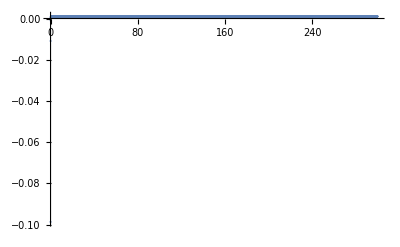

0.298531

-985.099

```mathematica
tab=Table[{τ,Exp[-η^2 τ] ψB.ψAτ[τ]},{τ,0,300,0.05}];
ListPlot[tab,PlotRange->All]
f=Interpolation[tab];
NIntegrate[f[x],{x,0,300},MaxRecursion->20]
%-Re[A1]
```

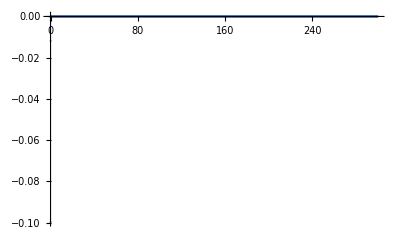

-0.00261251

-0.00035554

```mathematica
tab=Table[{τ,Exp[-η^2 τ] ψBp.ψApτ[τ]},{τ,0,300,0.05}];
ListPlot[tab,PlotRange->All]
f=Interpolation[tab];
NIntegrate[f[x],{x,0,300},MaxRecursion->20]
%-Re[A2]
```

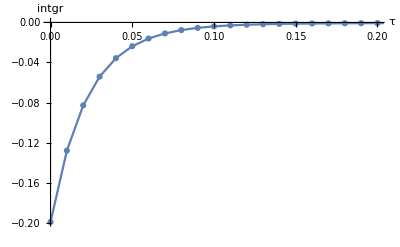

tau.pdf

-0.00484116

-0.00486371

0.0000225473

-0.00463584

```mathematica
tab=Table[{τ,Exp[-η^2 τ]( ψB.ψAτ[τ]+ψBp.ψApτ[τ])},{τ,0,0.5,0.01}];
ListPlot[tab,PlotRange->{{0,0.2},All},AxesLabel->{"τ","intgr"},LabelStyle->Larger,Joined->True,Mesh->True]
Export["tau.pdf",%]
f=Interpolation[tab];
res=NIntegrate[f[x],{x,0,0.5},MaxRecursion->20]
Re[A1+A2]
abserror=(res-Re[A1+A2])
relerror=abserror/Re[A1+A2]
```

```mathematica
Re[A1+A2]
resDMRG=-0.0048637
(resDMRG-Re[A1+A2])/Re[A1+A2]
```

-0.00486371

-0.0048637

-1.0418×10^-6

```mathematica
TableForm[tab]
```

0. | -0.199399
0.01 | -0.128033
0.02 | -0.0828963
0.03 | -0.0541436
0.04 | -0.0357007
0.05 | -0.0237909
0.06 | -0.0160488
0.07 | -0.0109827
0.08 | -0.00764507
0.09 | -0.00543048
0.1 | -0.00394957
0.11 | -0.00295051
0.12 | -0.00226953
0.13 | -0.00179963
0.14 | -0.00147053
0.15 | -0.00123589
0.16 | -0.00106501
0.17 | -0.000937493
0.18 | -0.000839719
0.19 | -0.00076256
0.2 | -0.000699878
0.21 | -0.000647523
0.22 | -0.000602677
0.23 | -0.000563417
0.24 | -0.000528415
0.25 | -0.000496753
0.26 | -0.000467784
0.27 | -0.000441047
0.28 | -0.000416209
0.29 | -0.000393022
0.3 | -0.0003713
0.31 | -0.000350896
0.32 | -0.000331695
0.33 | -0.0003136
0.34 | -0.000296531
0.35 | -0.000280417
0.36 | -0.000265199
0.37 | -0.000250819
0.38 | -0.000237229
0.39 | -0.000224383
0.4 | -0.000212238
0.41 | -0.000200754
0.42 | -0.000189895
0.43 | -0.000179626
0.44 | -0.000169915
0.45 | -0.000160731
0.46 | -0.000152045
0.47 | -0.00014383
0.48 | -0.00013606
0.49 | -0.000128712
0.5 | -0.000121761

```mathematica
Exp[-η^2 0.5]
```

1.